### naloga 2

```mathematica
sez={10,20,30,40,50,60,70}
```

{10,20,30,40,50,60,70}

```mathematica
sez = Table[x*10,{x,7}]
```

{10,20,30,40,50,60,70}

```mathematica
Take[sez, 3]
```

{10,20,30}

```mathematica
Take[sez,-2]
```

{60,70}

```mathematica
Take[sez,{2,4}]
```

{20,30,40}

```mathematica
Part[sez,{2,3,5}]
```

{20,30,50}

```mathematica
Drop [sez,{4,5}]
```

{10,20,30,60,70}

```mathematica
naloga 3
```

```mathematica
ClearAll[x,a]
```

```mathematica
sez={x^6, x^2, a}
```

{x^6,x^2,a}

```mathematica
sez/.x->3
```

{729,9,a}

```mathematica
sez/.x->x^2
```

{x^12,x^4,a}

```mathematica
sez/.x^2->x
```

{x^6,x,a}

```mathematica
sez/.x->{1,2,3}
```

{{1,64,729},{1,4,9},a}

```mathematica
sez/.{x->3,a->x}
```

{729,9,x}

```mathematica
Replace
```

```mathematica
naloga 4
```

```mathematica
D[x^5+4x^3-9,x]/.x->{1,5}
```

{17,3425}

```mathematica
FullSimplify[D[Abs[x+1],x],x∈Reals]
```

Sign[1+x]

```mathematica
resitev =FullSimplify[D[Abs[x+1],x],x∈Reals]
```

```mathematica
naloga 5
```

```mathematica
f[x_]:=x^3Log[4x+5]
```

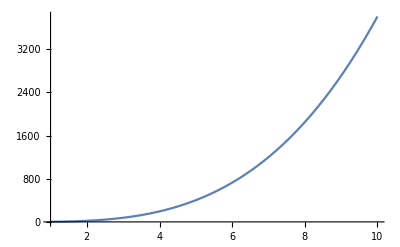

```mathematica
Plot [f[x], {x,1,10}]
```

```mathematica
x0=5
```

5

```mathematica
f[x0]
```

125 Log[25]

```mathematica
k0=D[f[x],x]/.x->x0
```

20+75 Log[25]

```mathematica
Solve[f[x0]=k0*x0+n,n]
```

Solve::naqs: n+5 (20+75 Log[25]) is not a quantified system of equations and inequalities.

Solve[n+5 (20+75 Log[25]),n]